```mathematica
Clear[Act];
Act[{{a_,b_},{c_,d_}}, tau_]:=(a tau+b)/(c tau+d);
```

```mathematica
(* https://doc.sagemath.org/html/en/reference/arithgroup/sage/modular/arithgroup/arithgroup_perm.html *)
s2 = {{0,-1},{1,0}};
s3 = {{0,1},{-1,1}};
l = {{1,1},{0,1}};
r = {{1,0},{1,1}};
```

```mathematica
Act[s2,tau]
```

-1/tau

```mathematica
Act[s3,tau]
```

1/(1-tau)

```mathematica
Act[l,tau]
```

1+tau

```mathematica
Act[r,tau]
```

tau/(1+tau)

```mathematica
r==Inverse[s2].Inverse[l].s2
```

True

```mathematica
MatrixPower[s2.l,2]
```

{{-1,-1},{1,0}}

```mathematica
sigS=Cycles[{{1,8},{2,4},{5,7},{3,9},{6,10}}];
sigR=Cycles[{{8,2,5},{4,3,9},{7,6,10}}];
sigT=Cycles[{{1,2,3,4,5,6,7,8},{9},{10}}];
```

```mathematica
sigS\[PermutationProduct]sigR
```

Cycles[{{1,2,3,4,5,6,7,8}}]

```mathematica
sigR\[PermutationProduct]sigS
```

Cycles[{{1,8,4,9,2,7,10,5}}]

```mathematica
BorisS=s2
```

{{0,-1},{1,0}}

```mathematica
BorisR = s2.l
```

{{0,-1},{1,1}}

```mathematica
BorisT=l
```

{{1,1},{0,1}}

```mathematica
BorisR==BorisS.BorisT
```

True

```mathematica
BorisT==-BorisS.BorisR
```

True

```mathematica
sigS\[PermutationProduct]sigR==sigT//Simplify
```

True

```mathematica
sigS\[PermutationProduct]sigT
```

Cycles[{{2,5,8},{3,9,4},{6,10,7}}]

```mathematica
sigR
```

Cycles[{{2,5,8},{3,9,4},{6,10,7}}]

```mathematica
Act[BorisT,tau]
```

1+tau

```mathematica
Act[BorisS,tau]
```

-1/tau

```mathematica
BorisS.BorisT
```

{{0,-1},{1,1}}

```mathematica
BorisR
```

{{0,-1},{1,1}}

```mathematica
-I PauliMatrix[2]
```

{{0,-1},{1,0}}

```mathematica
Act[BorisR,tau]
```

-1/(1+tau)

## fundamental domain

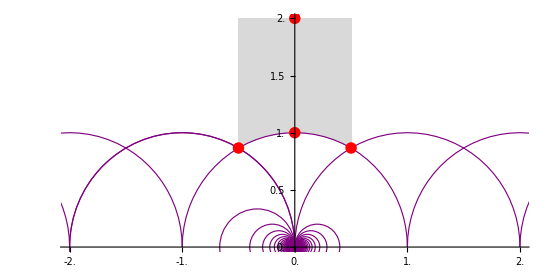

```mathematica
Show[
RegionPlot[tau1^2+tau2^2>=1&&-1/2<=tau1<=1/2, {tau1,-2,2},{tau2,0,2},
PlotStyle->LightGray,
BoundaryStyle->None,
PlotPoints->40,
GridLines->{{-5/2,-3/2,-1/2,1/2,3/2,5/2}, None},
GridLinesStyle->Directive[Purple, Thickness[.0015]],
AspectRatio->Automatic,
Frame->False,
Axes->True,
Ticks->N@{Table[i,{i,-2,2,1/2}],Table[i,{i,0,2,1/4}]},
PlotRange->{{-2,2},{0,2}}
],
Graphics[{Purple, Thickness[.0015], 
Circle[{0,0},1,{0,Pi}],
Circle[{-1,0},1,{0,Pi}],
Circle[{1,0},1,{0,Pi}],
Circle[{-2,0},1,{0,Pi}],
Circle[{2,0},1,{0,Pi}],
Circle[{-3,0},1,{0,Pi}],
Circle[{3,0},1,{0,Pi}],
Table[If[n==1||n==0,Nothing,Circle[{1/(2n+1),0},1/Abs[2n+1]], {0,Pi}], {n,-50,50}]
}],
Graphics[{Red,PointSize[.015],Point[ReIm/@{Exp[2Pi I/3], Exp[I Pi/3], I, 2I}]}]
]
```

```mathematica
Simplify@ComplexExpand[Re[(a tau+b)/(c tau+d)/.{tau->s+I t}]]
```

(a d s+b (d+c s)+a c (s^2+t^2))/(d^2+2 c d s+c^2 (s^2+t^2))